```mathematica
SetDirectory["~/maths/ibmer/papers/mdgp/intro_dg/mathematica"]
```

/Users/liberti/maths/ibmer/papers/mdgp/intro_dg/mathematica

```mathematica
Get["ApproxRealize.m"]
```

```mathematica
Get["ProjectionTools.m"]
```

```mathematica
G=Graph[{1<->2,1<->3,2<->3,2<->4,3<->4},VertexLabels->"Name",EdgeWeight->{2,2,1,1,1}]
```

-Graphics-

```mathematica
GraphDistanceMatrix[G]
```

{{0.,2.,2.,3.},{2.,0.,1.,1.},{2.,1.,0.,1.},{3.,1.,1.,0.}}

```mathematica
n = 40; m =Round[N[0.5*n (n-1)/2]]; G=RandomGraph[{n,m},EdgeWeight->RandomReal[{0,5},m]]
```

-Graphics-

```mathematica
GraphPlot3D[G, EdgeRenderingFunction->({GrayLevel[0.5], Line[#1]}&), VertexRenderingFunction->(Sphere[#1, .05]&), VertexCoordinateRules-> Isomap[G,3]]
```

-Graphics3D-

```mathematica
S = SpiralGraph[]
```

-Graphics3D-

```mathematica
xHigh = LiftRandomRotate[Realization[S], 30]; GraphPlot3D[S, VertexCoordinateRules-> Isomap[S,3]]
```

-Graphics3D-

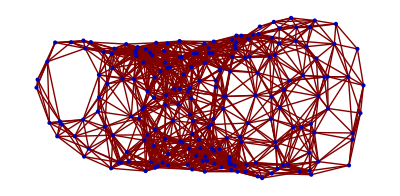

```mathematica
GraphPlot[S, VertexCoordinateRules->Isomap[S, 2]]
```

```mathematica
A = Normal[WeightedAdjacencyMatrix[S]];
```

```mathematica
pos = Flatten[Position[A[[2]], x_ /;x > 0]]
```

{1,3,4,5,33,34,36}

```mathematica
Zi = Map[(x[[#]] - x[[3]])&, pos]
```

{{-0.575592,-0.159504},{0.,0.},{0.434955,-0.0479538},{0.0975812,-0.171159},{-1.00903,-0.447079},{-0.599492,-0.297283},{-0.218229,-0.189856}}

```mathematica
Ci = Transpose[Zi].Zi
```

{{1.95516,0.725016},{0.725016,0.381339}}

```mathematica
Tr[Ci]
```

2.3365

```mathematica
$Path
```

{/Applications/Mathematica.app/SystemFiles/Links,/Users/liberti/Library/Mathematica/Kernel,/Users/liberti/Library/Mathematica/Autoload,/Users/liberti/Library/Mathematica/Applications,/Library/Mathematica/Kernel,/Library/Mathematica/Autoload,/Library/Mathematica/Applications,.,/Users/liberti,/Applications/Mathematica.app/AddOns/Packages,/Applications/Mathematica.app/AddOns/LegacyPackages,/Applications/Mathematica.app/SystemFiles/Autoload,/Applications/Mathematica.app/AddOns/Autoload,/Applications/Mathematica.app/AddOns/Applications,/Applications/Mathematica.app/AddOns/ExtraPackages,/Applications/Mathematica.app/SystemFiles/Kernel/Packages,/Applications/Mathematica.app/Documentation/English/System,/Applications/Mathematica.app/SystemFiles/Data/ICC}

```mathematica
AppendTo[$Path, "~/work/mathematica"]
```

{/Applications/Mathematica.app/SystemFiles/Links,/Users/liberti/Library/Mathematica/Kernel,/Users/liberti/Library/Mathematica/Autoload,/Users/liberti/Library/Mathematica/Applications,/Library/Mathematica/Kernel,/Library/Mathematica/Autoload,/Library/Mathematica/Applications,.,/Users/liberti,/Applications/Mathematica.app/AddOns/Packages,/Applications/Mathematica.app/AddOns/LegacyPackages,/Applications/Mathematica.app/SystemFiles/Autoload,/Applications/Mathematica.app/AddOns/Autoload,/Applications/Mathematica.app/AddOns/Applications,/Applications/Mathematica.app/AddOns/ExtraPackages,/Applications/Mathematica.app/SystemFiles/Kernel/Packages,/Applications/Mathematica.app/Documentation/English/System,/Applications/Mathematica.app/SystemFiles/Data/ICC,~/work/mathematica}

```mathematica
Needs["Convex`ConvexPolyhedra`"]
```

```mathematica
?ConvexPolyhedron
```

ConvexPolyhedron is the head of an expression denoting a closed convex polyhedron.

```mathematica
P = EmptyPolyhedron[3]
```

ConvexPolyhedron[ConvexCone[4,{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{},{},{}]]

```mathematica
P = AddPointToPolyhedron[P, {1,0,0}]
```

ConvexPolyhedron[ConvexCone[4,{},{{1,1,1,-1},{0,0,-1,0},{0,-1,0,0},{-1,0,0,0}},{},{{0,0,0,1},{0,0,1,1},{0,1,0,1},{1,0,0,1}}]]

```mathematica
Halfspaces[P]
```

{{1,1,1,-1},{0,0,-1,0},{0,-1,0,0},{-1,0,0,0}}